```mathematica
Biseccion[a_,b_,Tol_,n_,G_]:=
Module[{i=1,a1=a,b1=b,X=(a+b)/2},
	While[i≤n,
	X=(a1+b1)/2;
			If[(G[X]==0)||(Abs[b1-a1]/2<Tol),N[X,25],
		Print["En la iteracion ",i," el valor de X es ",N[X,10]];
Print["El valor de a es: ",a1];
Print["El valor de b es: ",b1];

];
i++;

If[G[a1]*G[X]>0,a1=X,b1=X];
];

If[i>n+1,Print["El numero de iteraciones ha sido excedido"]];
];
```

```mathematica
G[x_]:=ArcTan[x^2+1]-2 x^2+x;
```

```mathematica
N[Biseccion[0,2,0.1,20,G],5]
```

En la iteracion 1 el valor de X es 1.

En la iteracion el valor de a es: 0

En la iteracion el valor de b es: 2

En la iteracion 2 el valor de X es 1.5

En la iteracion el valor de a es: 1

En la iteracion el valor de b es: 2

En la iteracion 3 el valor de X es 1.25

En la iteracion el valor de a es: 1

En la iteracion el valor de b es: 3/2

En la iteracion 4 el valor de X es 1.125

En la iteracion el valor de a es: 1

En la iteracion el valor de b es: 5/4

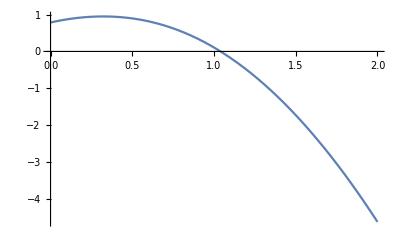

```mathematica
Plot[ArcTan[x^2+1]-2 x^2+x,{x,0,2}]
```